# Chapter 39

```mathematica
Round[{x,x+1,x+2,x^2}]/.x->RandomReal[100]
```

{47,48,49,2251}

```mathematica
Round[{x,x+1,x+2,x^2}]/.x:> RandomReal[100]
```

{85,23,14,2216}

# Chapter 40

```mathematica
f[x_]:=x^2
f[2]
```

4

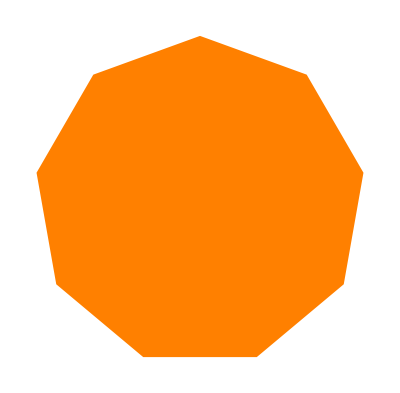

```mathematica
poly[X_]:=Graphics[Style[RegularPolygon[X],Orange]]
poly[9]
```

```mathematica
f[X_,y_]:=Reverse[{X,y}]
f[cat,bat]
```

{bat,cat}

```mathematica
f[X_,y_]:=X*y/x+y
f[2,5]
```

10

```mathematica
f[X_,y_]:={X+y,X-y,X/y}
f[2,5]
```

{7,-3,2/5}

```mathematica
evenodd[x_]:=If[x==0,Red,If[EvenQ[x],Black,White]]
evenodd[0]
evenodd[5]
evenodd[6]
```

RGBColor[1, 0, 0]

GrayLevel[1]

GrayLevel[0]

```mathematica
f[x_,y_,z_]:=If[x==1,y+z,If[x==2,y*z,x^y]]
f[1,5,6]
f[2,5,6]
f[3,5,6]
```

11

30

243

```mathematica
f[x_]:=If[x==1||x==0,1,f[x-1]+f[x-2]]
f[10]
```

89

```mathematica
animal[x_]:=Interpreter["Animal"][x]["Image"]
animal["cat"]
```

-Graphics-

```mathematica
nearwords[x_,y_]:=Nearest[WordList[],x,y]
```

```mathematica
nearwords["cat",3]
```

{cat,at,bat}